# Title

Author Name

Abstract

## Section

XXXX:

## Notes

Some statements come to us in the form.

Let n∈ℕ, or .

```mathematica
PositiveIntegers
```

(∀n≥M)(P(n)).

But we don't have to start with m.

For this we have the extended principle/principal of mathematical induction.

Let m be an integer. m∈ℤ.

If T is a subset of ℕ such that: T⊂ℕ

M∈T

∀ k ∈ℕ with k≥M, if k∈T then k+1∈T. if P(k) is true.

Then T contains all integers greater than or equal to M.

What is the link between this nice principle and P(n)?

principle

WolframAlphaQueryResults

We want to show the elements are related in what way.

We want to show that the elements in T make P(n) true!

How do we use this?

induction

WolframAlphaQueryResults

## Proof Example

How do we use this prove

(∀ n ∈ Integers, with n≥M)(P(n)).

Step 1: prove P(M) is true. (Anchor, basis, bottom ladder rung)

Step 2:Prove for k≥M, if P(k) is true then P(k+1) is true.

Step 3: Prove23 P(n) is true for n≥M.

Example:

Proposition: For all n∈ℕ, with n≥2, 3^1>1+2^n

```mathematica
FindInstance[3^n>1+2^n,{n},Integers]
```

{{n→198}}

Proof by induction:

Proposition: For All n ∈ N, 3^n>1+2^n:P(n).

From our above notation M=2.

First verify that P(n) holds for n=2.

```mathematica
And[Or[p,q],r]//BooleanConvert
```

(p&&r)||(q&&r)

```mathematica
Or[And[p,q],r]//BooleanConvert
```

(p&&q)||r

```mathematica
SameQ[p∨q∧r,p∧q∨r]
```

False

For the LHS we have 3^2=9

For the RHS we have 2^2+1=5

Since 9>5, P(2) is true.

Let P(k) be true for k≥2.

3^k>2^k+1

We want to show that 3^(k+1)>2^(k+1)+1 is true. This will show that P(k+1) is true.

```mathematica
3^(k+1)/3^k
```

3

```mathematica
(2^(k+1)+1)/(2^k+1)
```

(1+2^(1+k))/(1+2^k)

```mathematica
FullSimplify[(1+2^(1+k))/(1+2^k)]
```

2-1/(1+2^k)

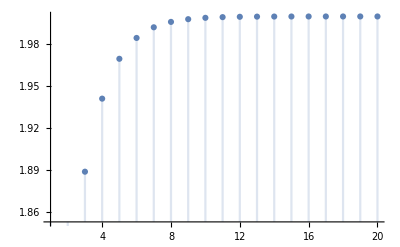

```mathematica
DiscretePlot[2-1/(1+2^k),{k,1,20}]
```

```mathematica
PowerExpand[3^(k+1)>2^(k+1)+1]
```

3^(1+k)>1+2^(1+k)

```mathematica
(3(3^k>2^k+1))//ExpandAll
```

3 (3^k>1+2^k)

```mathematica
MultiplySides[3^k>2^k+1,3]
```

3^(1+k)>3 (1+2^k)

3^(k+1)>3*2^k+3

3^(k+1)>3*2^k+3>2*2^k+1

3^(k+1)>3*2^k+3>2^(k+1)+1

Therefore P(k+1) follows from P(k). true

Hence the PMI, 3^n>2^n+1 for n≥2 .

prove by pmi 3^(k)>2^(k)+1 for k>=2 and k integer

WolframAlphaQueryResults

```mathematica
Reduce[∀_(k,{k∈Integers,k>=2})3^k>=2^k+1]
```

True

```mathematica
Reduce[∀_(k,{k∈Integers,k>=2})3^k>2^k+1]
```

True

∀ n ∈ ℕ, n is a prime number or n is a composite #.

n is either prime or the product of primes.

With our previous proposition, we used the truth of P(k) to show that P(k+1) is also true. That is P(k+1) follows from P(k).

Let k=13.

```mathematica
PrimeQ[13]
```

True

```mathematica
MangoldtLambda[13]
```

Log[13]

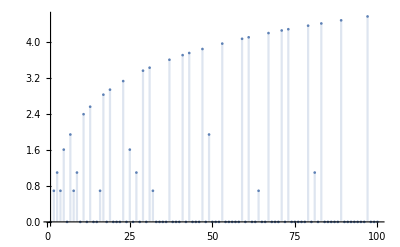

```mathematica
DiscretePlot[MangoldtLambda[n],{n,100}]
```

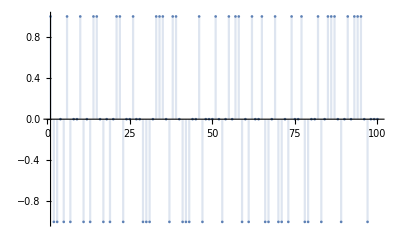

```mathematica
DiscretePlot[MoebiusMu[n],{n,100}]
```

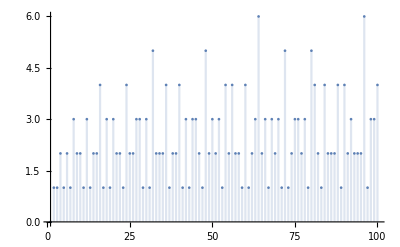

```mathematica
DiscretePlot[PrimeOmega[n],{n,100}]
```

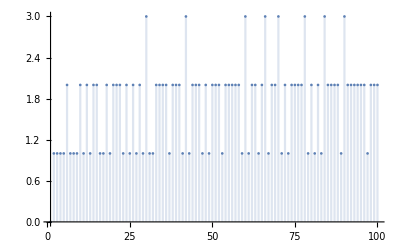

```mathematica
DiscretePlot[PrimeNu[n],{n,100}]
```

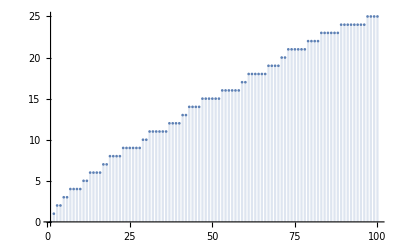

```mathematica
DiscretePlot[PrimePi[n],{n,100}]
```

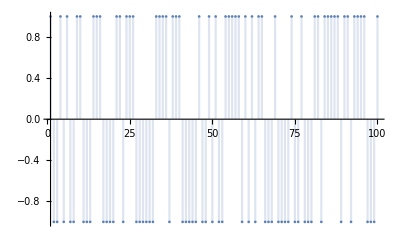

```mathematica
DiscretePlot[LiouvilleLambda[n],{n,100}]
```

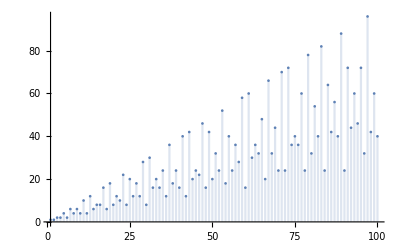

```mathematica
DiscretePlot[EulerPhi[n],{n,100}]
```

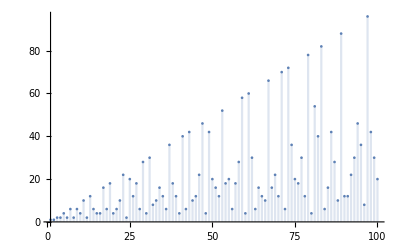

```mathematica
DiscretePlot[CarmichaelLambda[n],{n,100}]
```

Let k=13.

P(k)=P(13) is true since 13 is prime. We need to show that P(k+1)

```mathematica
Names["Prime*"]
```

{Prime,PrimeNu,PrimeOmega,PrimePi,PrimePowerQ,PrimeQ,Primes,PrimeZetaP}